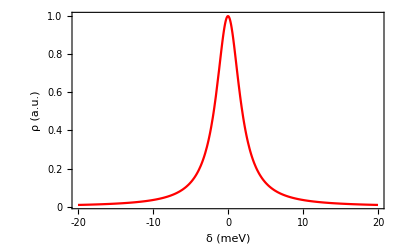
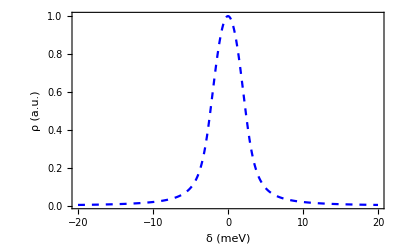

single_cavity.pdf

```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
texStyle={FontFamily->"Latin Modern Roman",FontSize->12,FontColor->Black};
SetOptions[Plot,BaseStyle->texStyle,Frame->True,Axes->False];
eqn1=0==-γR NR+P-G NR (ρ+1);
eqn2=0==-γ0 ρ+G NR(ρ+1);
sol1=Solve[eqn1,NR][[1]];
sol=ρ/.Solve[eqn2/.sol1,ρ][[2]];
γR=0.7;
γ0=4;
γv=2.9;
Γ=(γR+γ0+γv)/2;
ω0=2526;
ωv=194;
G=g^2 Γ/(δ^2+Γ^2/4);
P=30;
g=0.5;
solmax=sol/.δ->0;
Gmax=G/.δ->0;
ωR=δ+(ω0+ωv);
plot1=Plot[sol/solmax,{δ,-20,20},PlotStyle->Directive[Blue,Dashed],ImagePadding->{{50, 70}, {40, 20}},Frame->{True,True,True,False},FrameStyle->{Automatic,Blue,Automatic,Automatic},PlotRange->All,FrameLabel->{{"ρ (a.u.)","G Γ/(4g^2)"},{"δ (meV)",""}}];
plot2=Plot[G Γ/(4g^2),{δ,-20,20},PlotStyle->Directive[Red],ImagePadding->{{50, 70}, {40,20}},Axes->False,Frame->{False,False,False,True},FrameTicks->All,FrameStyle->{Automatic,Automatic,Automatic,Red},PlotRange->All,FrameLabel->{{"ρ (a.u.)","G Γ/(4g^2)"},{"δ (meV)",""}}];
Overlay[{plot2,plot1}]
Export["single_cavity.pdf",%]
```